```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3/datav3

```mathematica
(*dataall=Table[Import["./Shi_870-890_band=15_nodes=51/Shi_mu="<>ToString[i]<>"_m0=700.0-flag_4-51x104_VC=true.csv"],{i,880,890,5}];*)
dataall=Table[Import["./Shi_870-960_band=15_nodes=51/Shi_mu="<>ToString[i]<>"_m0=700.0-flag_4-51x104_VC=true.csv"],{i,870,960,5}];
```

```mathematica
n=Length[Table[i,{i,870,960,5}]]
```

19

```mathematica
dataall[[1]][[1]]
```

{T_mu,sigma,ω₀,n_B,P,e}

```mathematica
dataall[[1]][[2]]
```

{(17.0, 855.0071142042996),92.8641,0.0373279,0.00050769,0.00850413,0.425574}

```mathematica
Table[i,{i,17,120}]
```

{17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}

```mathematica
Length[%]
```

104

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*104+i]][[5]],{i,2,105}],{j,0,50}],{n1,1,19}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[870+(i-1)*5]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,19}],{j,1,51}];
```

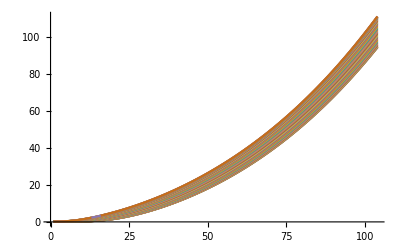

```mathematica
ListLinePlot[pdata[[1]]]
```